```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/xiaonuxiong/Dropbox/PDF Euclidean Lattice/Pion_PDF_Lattice/pion_PDF

```mathematica
<<XML`
```

# F(z)=⟨π(P)|ψ̄(0)L(0,z)ψ(z)|π(P)⟩

## P⃗=(0,0,0)

## z=1

```mathematica
FP0z1XMLdat=StringReplace[Import["pion_correlator"],{"\n"->"","<?xml version="~~x__~~"?>"->"","<PseudoScalar>"->"","</PseudoScalar>"->""}];
```

```mathematica
FP0z1tdat=Flatten[(ImportString[FP0z1XMLdat,"XML"]//.{XMLElement["re",{},{x__}],XMLElement["im",{},{y__}]}:>ToExpression[StringReplace[x,"e"->"*^"]]+I*ToExpression[StringReplace[y,"e"->"*^"]]//.{XMLElement["elem",{},y_]->y,XMLElement["OLattice",{},y_]->y})⟦2,-1,-1⟧]
```

{2.42844×10^-7+2.28784×10^-7 ⅈ,-6.01664×10^-7-2.66989×10^-7 ⅈ,-9.68339×10^-8-3.7635×10^-7 ⅈ,-5.14794×10^-9+3.13857×10^-8 ⅈ,5.45397×10^-9+7.52313×10^-9 ⅈ,4.67953×10^-11+3.887×10^-9 ⅈ,-4.15053×10^-11+4.77529×10^-10 ⅈ,-4.18408×10^-12+9.98501×10^-11 ⅈ,-4.56218×10^-12+1.3967×10^-11 ⅈ,-4.66816×10^-13+1.63802×10^-12 ⅈ,-4.82298×10^-14+1.59356×10^-13 ⅈ,3.47904×10^-15+1.27332×10^-14 ⅈ,-2.37997×10^-16+2.62193×10^-15 ⅈ,1.51554×10^-16+4.30143×10^-16 ⅈ,2.54812×10^-17+6.93203×10^-17 ⅈ,3.00772×10^-20+1.03436×10^-17 ⅈ,-8.10864×10^-19+1.49705×10^-18 ⅈ,-6.4773×10^-18+1.40999×10^-17 ⅈ,3.57837×10^-18+1.20581×10^-16 ⅈ,4.00993×10^-16+1.23565×10^-16 ⅈ,1.92708×10^-15+8.25517×10^-16 ⅈ,4.03459×10^-15-7.6256×10^-15 ⅈ,7.31853×10^-14+3.64941×10^-14 ⅈ,3.17919×10^-13-1.82762×10^-13 ⅈ,4.9122×10^-12+8.29816×10^-13 ⅈ,2.39995×10^-11+1.48846×10^-11 ⅈ,9.53636×10^-11-7.50037×10^-11 ⅈ,9.69786×10^-10-8.48637×10^-10 ⅈ,8.45482×10^-9-4.30398×10^-9 ⅈ,6.87825×10^-8-4.68879×10^-8 ⅈ,4.57399×10^-7-2.59845×10^-7 ⅈ,8.95844×10^-7-3.11921×10^-6 ⅈ}

```mathematica
FP0zm1XMLdat=StringReplace[Import["pion_correlator"],{"\n"->"","<?xml version="~~x__~~"?>"->"","<PseudoScalar>"->"","</PseudoScalar>"->""}];
```

```mathematica
FP0zm1tdat=Flatten[(ImportString[FP0zm1XMLdat,"XML"]//.{XMLElement["re",{},{x__}],XMLElement["im",{},{y__}]}:>ToExpression[StringReplace[x,"e"->"*^"]]+I*ToExpression[StringReplace[y,"e"->"*^"]]//.{XMLElement["elem",{},y_]->y,XMLElement["OLattice",{},y_]->y})⟦2,-1,-1⟧]
```

{2.42844×10^-7+2.28784×10^-7 ⅈ,-6.01664×10^-7-2.66989×10^-7 ⅈ,-9.68339×10^-8-3.7635×10^-7 ⅈ,-5.14794×10^-9+3.13857×10^-8 ⅈ,5.45397×10^-9+7.52313×10^-9 ⅈ,4.67953×10^-11+3.887×10^-9 ⅈ,-4.15053×10^-11+4.77529×10^-10 ⅈ,-4.18408×10^-12+9.98501×10^-11 ⅈ,-4.56218×10^-12+1.3967×10^-11 ⅈ,-4.66816×10^-13+1.63802×10^-12 ⅈ,-4.82298×10^-14+1.59356×10^-13 ⅈ,3.47904×10^-15+1.27332×10^-14 ⅈ,-2.37997×10^-16+2.62193×10^-15 ⅈ,1.51554×10^-16+4.30143×10^-16 ⅈ,2.54812×10^-17+6.93203×10^-17 ⅈ,3.00772×10^-20+1.03436×10^-17 ⅈ,-8.10864×10^-19+1.49705×10^-18 ⅈ,-6.4773×10^-18+1.40999×10^-17 ⅈ,3.57837×10^-18+1.20581×10^-16 ⅈ,4.00993×10^-16+1.23565×10^-16 ⅈ,1.92708×10^-15+8.25517×10^-16 ⅈ,4.03459×10^-15-7.6256×10^-15 ⅈ,7.31853×10^-14+3.64941×10^-14 ⅈ,3.17919×10^-13-1.82762×10^-13 ⅈ,4.9122×10^-12+8.29816×10^-13 ⅈ,2.39995×10^-11+1.48846×10^-11 ⅈ,9.53636×10^-11-7.50037×10^-11 ⅈ,9.69786×10^-10-8.48637×10^-10 ⅈ,8.45482×10^-9-4.30398×10^-9 ⅈ,6.87825×10^-8-4.68879×10^-8 ⅈ,4.57399×10^-7-2.59845×10^-7 ⅈ,8.95844×10^-7-3.11921×10^-6 ⅈ}

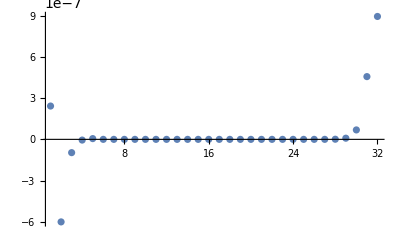

```mathematica
ListPlot[FP0z1tdat//Re,PlotRange->All]
```

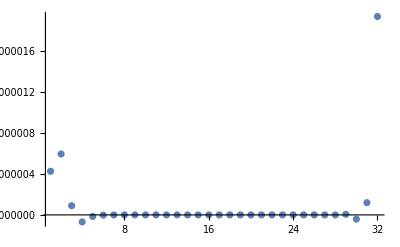

```mathematica
ListPlot[FP0z1tdat//Im,PlotRange->All]
```

## z=-1

```mathematica
FP0zm1XMLdat=StringReplace[Import["pion_correlator"],{"\n"->"","<?xml version="~~x__~~"?>"->"","<PseudoScalar>"->"","</PseudoScalar>"->""}];
```

```mathematica
FP0zm1tdat=Flatten[(ImportString[FP0zm1XMLdat,"XML"]//.{XMLElement["re",{},{x__}],XMLElement["im",{},{y__}]}:>ToExpression[StringReplace[x,"e"->"*^"]]+I*ToExpression[StringReplace[y,"e"->"*^"]]//.{XMLElement["elem",{},y_]->y,XMLElement["OLattice",{},y_]->y})⟦2,-1,-1⟧]
```

{1.70754×10^-8+4.26928×10^-7 ⅈ,-2.68166×10^-6+5.96293×10^-7 ⅈ,-7.10564×10^-8+9.×10^-8 ⅈ,-1.21443×10^-7-6.85628×10^-8 ⅈ,-7.45882×10^-9-1.50731×10^-8 ⅈ,-1.05163×10^-10-2.21236×10^-9 ⅈ,1.06892×10^-10-2.65586×10^-10 ⅈ,9.33065×10^-12-5.22294×10^-11 ⅈ,8.09125×10^-12-7.00251×10^-12 ⅈ,1.53816×10^-12-1.18694×10^-12 ⅈ,3.21086×10^-14-1.07741×10^-13 ⅈ,-4.97214×10^-15-6.16649×10^-15 ⅈ,-3.19661×10^-15-2.77558×10^-16 ⅈ,-1.0756×10^-16-4.21022×10^-16 ⅈ,-1.29202×10^-17-8.618×10^-17 ⅈ,-1.20166×10^-17-9.648×10^-18 ⅈ,-8.02602×10^-18-2.16827×10^-18 ⅈ,-2.88935×10^-17+2.00807×10^-18 ⅈ,-8.52217×10^-17+3.33433×10^-17 ⅈ,-5.42474×10^-16+3.09579×10^-16 ⅈ,-1.78574×10^-15+2.0829×10^-15 ⅈ,-2.20227×10^-15+1.80208×10^-14 ⅈ,2.21347×10^-14+2.24845×10^-14 ⅈ,6.86399×10^-13+7.44728×10^-14 ⅈ,4.5911×10^-12-1.16821×10^-12 ⅈ,4.05092×10^-11-2.49553×10^-11 ⅈ,4.65191×10^-11-1.12715×10^-10 ⅈ,7.69252×10^-10-2.64827×10^-10 ⅈ,3.59399×10^-9+5.84822×10^-9 ⅈ,6.78979×10^-8-4.17951×10^-8 ⅈ,6.83081×10^-7+1.19286×10^-7 ⅈ,1.58816×10^-6+1.94237×10^-6 ⅈ}

```mathematica
FP0zm1XMLdat=StringReplace[Import["pion_correlator"],{"\n"->"","<?xml version="~~x__~~"?>"->"","<PseudoScalar>"->"","</PseudoScalar>"->""}];
```

```mathematica
FP0zm1tdat=Flatten[(ImportString[FP0zm1XMLdat,"XML"]//.{XMLElement["re",{},{x__}],XMLElement["im",{},{y__}]}:>ToExpression[StringReplace[x,"e"->"*^"]]+I*ToExpression[StringReplace[y,"e"->"*^"]]//.{XMLElement["elem",{},y_]->y,XMLElement["OLattice",{},y_]->y})⟦2,-1,-1⟧]
```

{1.70754×10^-8+4.26928×10^-7 ⅈ,-2.68166×10^-6+5.96293×10^-7 ⅈ,-7.10564×10^-8+9.×10^-8 ⅈ,-1.21443×10^-7-6.85628×10^-8 ⅈ,-7.45882×10^-9-1.50731×10^-8 ⅈ,-1.05163×10^-10-2.21236×10^-9 ⅈ,1.06892×10^-10-2.65586×10^-10 ⅈ,9.33065×10^-12-5.22294×10^-11 ⅈ,8.09125×10^-12-7.00251×10^-12 ⅈ,1.53816×10^-12-1.18694×10^-12 ⅈ,3.21086×10^-14-1.07741×10^-13 ⅈ,-4.97214×10^-15-6.16649×10^-15 ⅈ,-3.19661×10^-15-2.77558×10^-16 ⅈ,-1.0756×10^-16-4.21022×10^-16 ⅈ,-1.29202×10^-17-8.618×10^-17 ⅈ,-1.20166×10^-17-9.648×10^-18 ⅈ,-8.02602×10^-18-2.16827×10^-18 ⅈ,-2.88935×10^-17+2.00807×10^-18 ⅈ,-8.52217×10^-17+3.33433×10^-17 ⅈ,-5.42474×10^-16+3.09579×10^-16 ⅈ,-1.78574×10^-15+2.0829×10^-15 ⅈ,-2.20227×10^-15+1.80208×10^-14 ⅈ,2.21347×10^-14+2.24845×10^-14 ⅈ,6.86399×10^-13+7.44728×10^-14 ⅈ,4.5911×10^-12-1.16821×10^-12 ⅈ,4.05092×10^-11-2.49553×10^-11 ⅈ,4.65191×10^-11-1.12715×10^-10 ⅈ,7.69252×10^-10-2.64827×10^-10 ⅈ,3.59399×10^-9+5.84822×10^-9 ⅈ,6.78979×10^-8-4.17951×10^-8 ⅈ,6.83081×10^-7+1.19286×10^-7 ⅈ,1.58816×10^-6+1.94237×10^-6 ⅈ}

```mathematica
ListPlot[FP0z1tdat//Re,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[FP0z1tdat//Im,PlotRange->All]
```

-Graphics-